# QuissoCircuit Tutorial

Basic usagepaclet:Q3/tutorial/QuissoCircuitTutorial#1868432623 | Examples with Controlled Gatespaclet:Q3/tutorial/QuissoCircuitTutorial#580366830
More Complicated Gatespaclet:Q3/tutorial/QuissoCircuitTutorial#2136908654 | Examples with Arbitrary Controlled Gatespaclet:Q3/tutorial/QuissoCircuitTutorial#87721419
With Inputs and Outputspaclet:Q3/tutorial/QuissoCircuitTutorial#94058740 | Quantum Fourier transformpaclet:Q3/tutorial/QuissoCircuitTutorial#31907961
Example with GraphStatespaclet:Q3/tutorial/QuissoCircuitTutorial#175892259 | Matrix on QuissoCircuitpaclet:Q3/tutorial/QuissoCircuitTutorial#462801707
Examples with Measurementspaclet:Q3/tutorial/QuissoCircuitTutorial#1921589536 | Matrix on QuissoCircuit: With Measurepaclet:Q3/tutorial/QuissoCircuitTutorial#991141748

QuissoCircuit provides the graphical representation of the quantum circuits.

QuissoCircuit | Graphical representation of quantum circuit
CNOT | Controlled NOT

XXXX.

## Basic usage

Elementary single qubit gates

```mathematica
<<Q3`Quisso`
```

```mathematica
Let[Qubit,S]
```

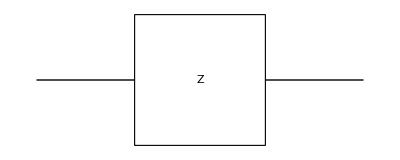

```mathematica
QuissoCircuit[S[1,3]]
```

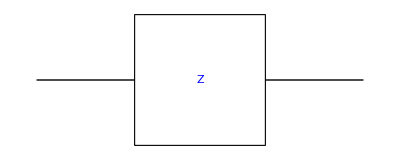

```mathematica
QuissoCircuit[Blue,S[1,3]]
```

```mathematica
QuissoCircuit[Ket[],S[1,3]]
```

-Graphics-

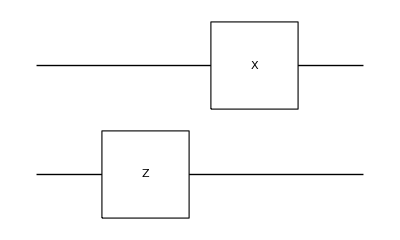

```mathematica
QuissoCircuit[S[2,3],S[1,1]]
```

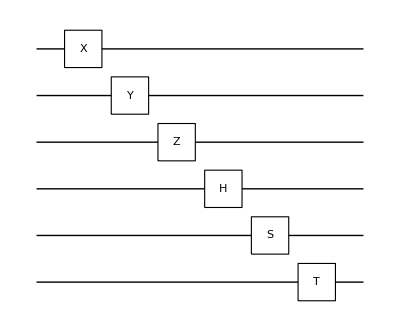

```mathematica
QuissoCircuit[S[1,1],S[2,2],S[3,3],S[4,6],S[5,7],S[6,8]]
```

“Spacer” is a special form to represent a time slice for no operation. It is useful for graphically extend certain time span. “Separator” puts a vertical dotted line to indicate a partiruclar time slice.

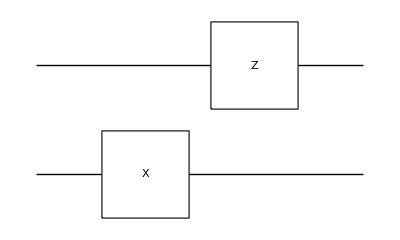

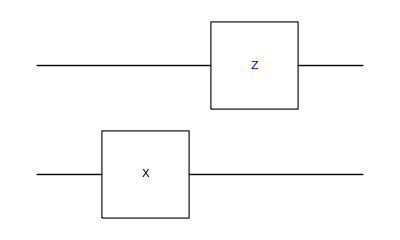

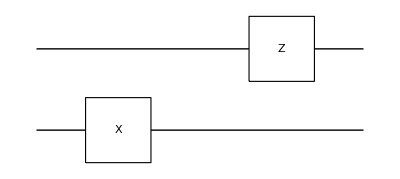

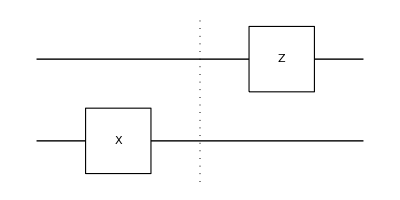

```mathematica
QuissoCircuit[S[2,1],S[1,3]]
QuissoCircuit[S[2,1],Blue,S[1,3]]
QuissoCircuit[S[2,1],"Spacer",S[1,3]]
QuissoCircuit[S[2,1],"Separator",S[1,3]]
```

QuissoExpression converts QuissoCircuit to usual Quisso expressions.

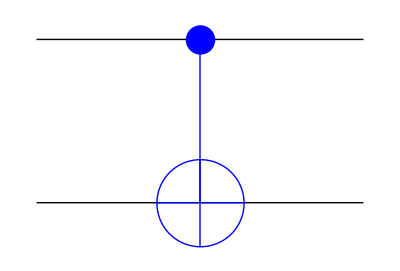

1/2-1/2 S_1^z S_2^x+S_1^z/2+S_2^x/2

```mathematica
qc=QuissoCircuit[Blue, CNOT[S[1],S[2]]]
QuissoExpression[qc]
```

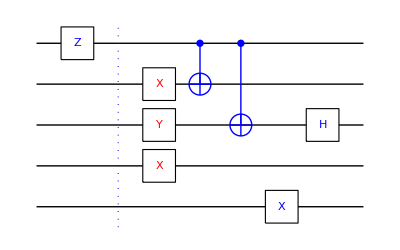

```mathematica
qc=QuissoCircuit[
Blue,S[1,3],"Separator",
{Red,S[2,1],S[3,2],S[4,1]},
{Blue, CNOT[S[1],S[2]] },
 CNOT[S[1],S[3]],
S[5,1],
S[3,6]]
```

```mathematica
expr=S[3,6]**S[5,1]**CNOT[S[1],S[3]]**CNOT[S[1],S[2]]**S[4,1]**S[3,2]**S[2,1]**S[1,3]//Simplify
```

-1/(2 √2)ⅈ (S_4^x S_5^x-S_1^z S_4^x S_5^x-ⅈ S_3^y S_4^x S_5^x+ⅈ S_1^z S_3^y S_4^x S_5^x+S_2^x S_3^x S_4^x S_5^x-S_2^x S_3^z S_4^x S_5^x+S_1^z S_2^x S_3^x S_4^x S_5^x-S_1^z S_2^x S_3^z S_4^x S_5^x)

```mathematica
qcExpr=QuissoExpression[qc]
qcExpr-expr//Simplify
```

-(ⅈ S_4^x S_5^x)/(2 √2)+(ⅈ S_1^z S_4^x S_5^x)/(2 √2)-(S_3^y S_4^x S_5^x)/(2 √2)+(S_1^z S_3^y S_4^x S_5^x)/(2 √2)-(ⅈ S_2^x S_3^x S_4^x S_5^x)/(2 √2)+(ⅈ S_2^x S_3^z S_4^x S_5^x)/(2 √2)-(ⅈ S_1^z S_2^x S_3^x S_4^x S_5^x)/(2 √2)+(ⅈ S_1^z S_2^x S_3^z S_4^x S_5^x)/(2 √2)

0

You can extend existing QuissoCircuit in a simple manner.

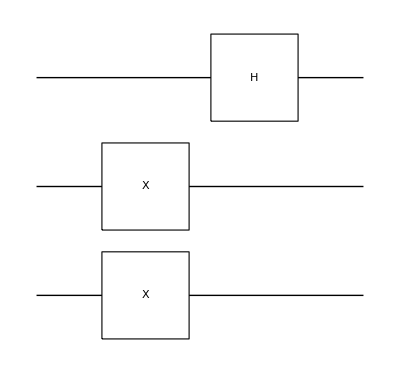

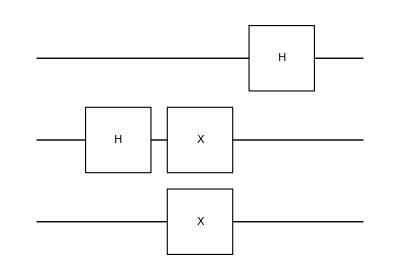

```mathematica
qc=QuissoCircuit[{S[2,1],S[3,1]},S[1,6]]
QuissoCircuit[S[2,6],qc]
```

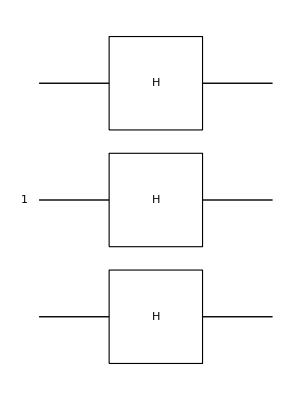

```mathematica
Clear[v]
nn=Range[1,3];
v[1]=Ket[S[2]->1];
QuissoCircuit[v[1],S[nn,6]]
```

0_S_10_S_20_S_3

0_S_1+1_S_1

0_S_2+1_S_2

0_S_3+1_S_3

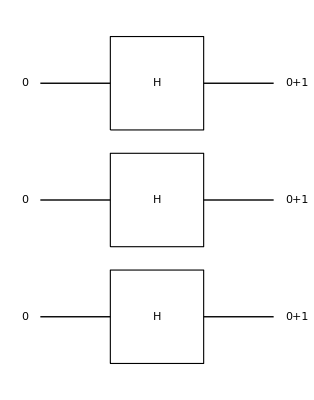

```mathematica
nn=Range[3];
v[1]=LogicalForm[Ket[],S[nn]]
v[2,1]=LogicalForm[Ket[]+Ket[S[1]->1]]
v[2,2]=LogicalForm[Ket[]+Ket[S[2]->1]]
v[2,3]=LogicalForm[Ket[]+Ket[S[3]->1]]
qc=QuissoCircuit[v[1],S[nn,6],v[2,1],v[2,2],v[2,3]]
```

```mathematica
expr=QuissoExpression[qc];
expr//LogicalForm
```

(0_S_10_S_20_S_3)/(2 √2)+(0_S_10_S_21_S_3)/(2 √2)+(0_S_11_S_20_S_3)/(2 √2)+(0_S_11_S_21_S_3)/(2 √2)+(1_S_10_S_20_S_3)/(2 √2)+(1_S_10_S_21_S_3)/(2 √2)+(1_S_11_S_20_S_3)/(2 √2)+(1_S_11_S_21_S_3)/(2 √2)

You can give custom labels.

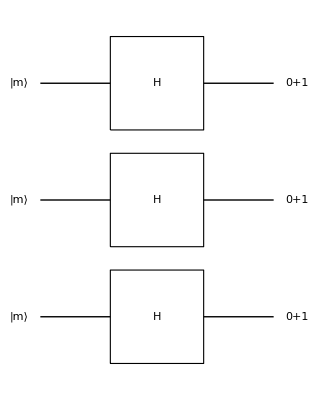

(0_S_10_S_20_S_3)/(2 √2)+(0_S_10_S_21_S_3)/(2 √2)+(0_S_11_S_20_S_3)/(2 √2)+(0_S_11_S_21_S_3)/(2 √2)+(1_S_10_S_20_S_3)/(2 √2)+(1_S_10_S_21_S_3)/(2 √2)+(1_S_11_S_20_S_3)/(2 √2)+(1_S_11_S_21_S_3)/(2 √2)

```mathematica
qc=QuissoCircuit[{v[1],Label->"|m⟩"},S[nn,6],v[2,1],v[2,2],v[2,3]]
expr=QuissoExpression@qc;LogicalForm@expr
```

If the custom label is a list, then its elements are rotated.

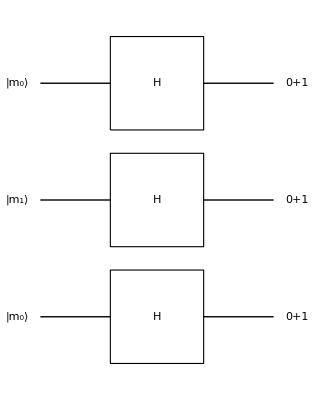

(0_S_10_S_20_S_3)/(2 √2)+(0_S_10_S_21_S_3)/(2 √2)+(0_S_11_S_20_S_3)/(2 √2)+(0_S_11_S_21_S_3)/(2 √2)+(1_S_10_S_20_S_3)/(2 √2)+(1_S_10_S_21_S_3)/(2 √2)+(1_S_11_S_20_S_3)/(2 √2)+(1_S_11_S_21_S_3)/(2 √2)

```mathematica
qc=QuissoCircuit[{v[1],Label->{"|m_0⟩","|m_1⟩"}},S[nn,6],v[2,1],v[2,2],v[2,3]]
expr=QuissoExpression@qc;
LogicalForm@expr
```

```mathematica
nn=Range[3];
v[1]=LogicalForm[Ket[],S[nn]]
v[2]=ProductState[S[nn]->{1,1}]
QuissoCircuit[v[1],S[nn,6],v[2]]
```

0_S_10_S_20_S_3

(0+1)_S_1⊗(0+1)_S_2⊗(0+1)_S_3

-Graphics-

Controlled-unitary gates

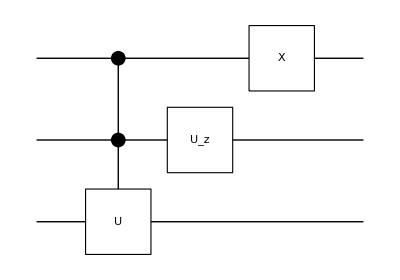

(1/8-ⅈ/16) (-3 ⅈ+√3) S_1^x S_2^z+1/16 (1-ⅈ √3) S_1^x S_3^y+1/16 ((-2-3 ⅈ)+(1+2 ⅈ) √3) S_1^y S_2^z+1/16 (ⅈ+√3) S_1^y S_3^y+1/16 ⅈ (ⅈ+√3) S_1^x S_2^z S_3^y+1/16 (-ⅈ-√3) S_1^y S_2^z S_3^y+1/16 ((3-2 ⅈ)+(6+ⅈ) √3) S_1^x+1/16 ((2+3 ⅈ)-(1+2 ⅈ) √3) S_1^y

(0 | 0 | 0 | 0 | 1/2 (-ⅈ+√3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/2 (-ⅈ+√3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/4 (3+ⅈ √3) | 1/4 (-ⅈ-√3)
0 | 0 | 0 | 0 | 0 | 0 | 1/4 (ⅈ+√3) | 1/4 (3+ⅈ √3)
1/2 (-ⅈ+√3) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/2 (-ⅈ+√3) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/2 (ⅈ+√3) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 (ⅈ+√3) | 0 | 0 | 0 | 0)

```mathematica
qc=QuissoCircuit[
Controlled[S[{1,2}],Rotation[S[3,2],Pi/3,Label->"U"],Label->"R"],
Rotation[S[2,3],Pi/3],
S[1,1]]
expr=QuissoExpression[qc]
mat=Simplify@Matrix[qc];
MatrixForm[mat]
```

## More Complicated Gates

```mathematica
<<Q3`Quisso`
```

```mathematica
Let[Qubit,S]
```

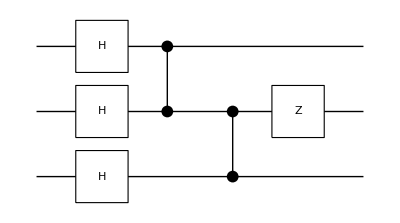

-Graphics-

{0.007017,Null}

{0.006647,Null}

-Graphics-

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
qc=QuissoCircuit[
S[{1,2,3},6],
CZ[S[1],S[2]],
CZ[S[2],S[3]],
S[2,3]
]
expr=QuissoExpression[qc]
Timing[mat1=Matrix[qc];]
Timing[mat2=Matrix[qc];]
mat2//MatrixForm
mat1-mat2//MatrixForm
```

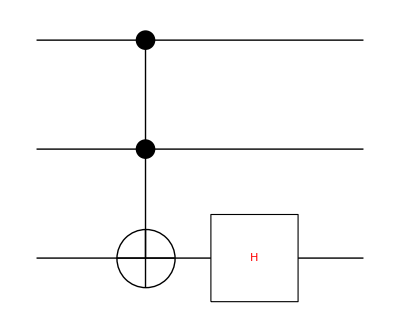

```mathematica
qc=QuissoCircuit[
Toffoli[S[1],S[2],S[3]],
Red,S[3,6]
]
```

```mathematica
qcExpr=QuissoExpression[qc]//Simplify
expr=S[3,6]**Toffoli[S[1],S[2],S[3]]//Simplify
qcExpr-expr//Simplify
```

1/(4 √2)(1+S_1^z S_2^z+S_1^z S_3^x-ⅈ S_1^z S_3^y+S_1^z S_3^z+S_2^z S_3^x-ⅈ S_2^z S_3^y+S_2^z S_3^z-S_1^z S_2^z S_3^x+ⅈ S_1^z S_2^z S_3^y-S_1^z S_2^z S_3^z-S_1^z-S_2^z+3 S_3^x+ⅈ S_3^y+3 S_3^z)

1/8 (√2+√2 S_1^z S_2^z+√2 S_1^z S_3^x-ⅈ √2 S_1^z S_3^y+√2 S_1^z S_3^z+√2 S_2^z S_3^x-ⅈ √2 S_2^z S_3^y+√2 S_2^z S_3^z-√2 S_1^z S_2^z S_3^x+ⅈ √2 S_1^z S_2^z S_3^y-√2 S_1^z S_2^z S_3^z-√2 S_1^z-√2 S_2^z+ⅈ √2 S_3^y+6 S_3^H)

3/8 (√2 S_3^x+√2 S_3^z-2 S_3^H)

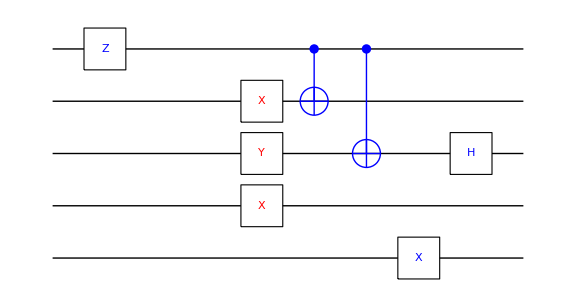

```mathematica
qc=QuissoCircuit[Blue,S[1,3],
"Spacer","Spacer",
{Red,S[2,1],S[3,2],S[4,1]},
{Blue, CNOT[S[1],S[2]] },
 CNOT[S[1],S[3]],
S[5,1],
S[3,6],
Opts->"A",
ImageSize->Large
]
```

```mathematica
qcExpr=QuissoExpression[qc]
expr=Multiply@@Reverse@{
S[1,3],S[2,1],S[3,2],S[4,1],CNOT[S[1],S[2]],CNOT[S[1],S[3]],S[5,1],S[3,6]}//Simplify
qcExpr-expr//Simplify
```

-(ⅈ S_4^x S_5^x)/(2 √2)+(ⅈ S_1^z S_4^x S_5^x)/(2 √2)-(S_3^y S_4^x S_5^x)/(2 √2)+(S_1^z S_3^y S_4^x S_5^x)/(2 √2)-(ⅈ S_2^x S_3^x S_4^x S_5^x)/(2 √2)+(ⅈ S_2^x S_3^z S_4^x S_5^x)/(2 √2)-(ⅈ S_1^z S_2^x S_3^x S_4^x S_5^x)/(2 √2)+(ⅈ S_1^z S_2^x S_3^z S_4^x S_5^x)/(2 √2)

-1/(2 √2)ⅈ (S_4^x S_5^x-S_1^z S_4^x S_5^x-ⅈ S_3^y S_4^x S_5^x+ⅈ S_1^z S_3^y S_4^x S_5^x+S_2^x S_3^x S_4^x S_5^x-S_2^x S_3^z S_4^x S_5^x+S_1^z S_2^x S_3^x S_4^x S_5^x-S_1^z S_2^x S_3^z S_4^x S_5^x)

0

## With Inputs and Outputs

You can specifies input and output states.

```mathematica
<<Q3`Quisso`
```

```mathematica
Let[Qubit,S]
Let[Real,a,b,c]
```

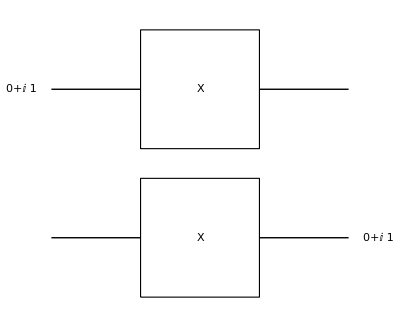

```mathematica
v[1]=Ket[]+I Ket[S[1]->1];
v[2]=Ket[]+I Ket[S[2]->1];
qc=QuissoCircuit[v[1],S[{1,2},1],v[2]]
```

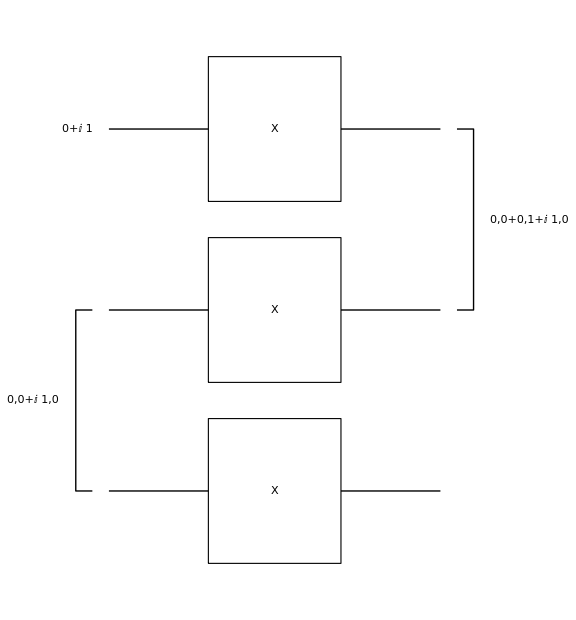

```mathematica
v[3]=LogicalForm[Ket[]+I Ket[S[1]->1]+Ket[S[2]->1],S[{1,2}]];
v[4]=LogicalForm[Ket[]+I Ket[S[2]->1],S[{2,3}]];
qc=QuissoCircuit[v[1],v[4],S[{1,2,3},1],v[3],ImageSize->Large]
```

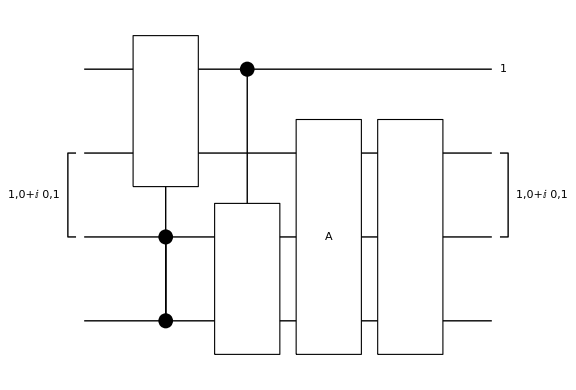

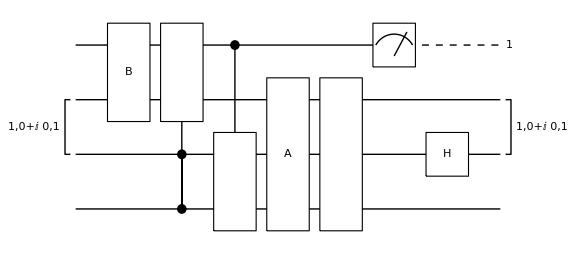

(1_S_1)/(2 √2)-(ⅈ 1_S_11_S_21_S_31_S_4)/(2 √2)+(ⅈ 1_S_11_S_2)/(2 √2)+(ⅈ 1_S_11_S_21_S_3)/(2 √2)+(ⅈ 1_S_11_S_21_S_4)/(2 √2)-(1_S_11_S_3)/(2 √2)-(1_S_11_S_31_S_4)/(2 √2)-(1_S_11_S_4)/(2 √2)

(0
0
0
0
0
0
0
0
1/(2 √2)
-1/(2 √2)
-1/(2 √2)
-1/(2 √2)
ⅈ/(2 √2)
ⅈ/(2 √2)
ⅈ/(2 √2)
-ⅈ/(2 √2))

```mathematica
Clear[expr,vec,mat];
expr[1]=S[2,1]+I S[4,3];
v[1]=Ket[S[2]->1]+ I Ket[S[3]->1];
mat[0]=ThePauli[1,3];
expr[2]=QuissoExpression[mat[0],S[{1,2}]];
qc=QuissoCircuit[v[1],
Controlled[S[{3,4}],S[1,1]-S[2,2]],
Controlled[S[1],S[3,2]+I S[4,1]],
{expr[1],Label->"A"},
expr[1],{Ket[S[1]->1],v[1]},
ImageSize->Large
]
qc=QuissoCircuit[{expr[2],Label->"B"},
qc,Measure[S[1]],S[3,6],
ImageSize->Large]
expr[0]=QuissoExpression[qc]
vec[0]=Matrix[qc];
vec[0]//MatrixForm
```

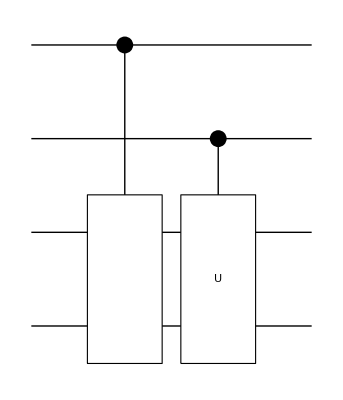

1/4+1/4 S_1^z S_2^z+1/2 ⅈ S_3^y S_4^x-1/2 S_1^z S_2^z S_3^y-1/2 ⅈ S_1^z S_2^z S_4^x-1/2 ⅈ S_1^z S_3^y S_4^x-1/2 ⅈ S_2^z S_3^y S_4^x+1/2 ⅈ S_1^z S_2^z S_3^y S_4^x+S_1^z/4+S_2^z/4+S_3^y/2+(ⅈ S_4^x)/2

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | -ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | -ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | 0 | 0 | ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⅈ | ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 | 0 | 0 | 0)

```mathematica
expr[1]=S[2,1]+I S[4,3];
qc=QuissoCircuit[
Controlled[S[1],S[3,2]+I S[4,1]],
Controlled[S[2],S[3,2]+I S[4,1],Label->"U"]
]
expr[0]=QuissoExpression[qc]
mat[0]=Matrix[qc];
mat[0]//MatrixForm
```

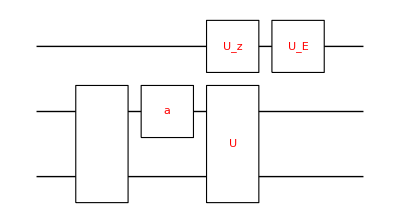

1/2 ⅈ (ⅈ+√3) Cos[b/2] Cos[1/2 (a+c+ϕ)] S_2^z+1/2 (ⅈ+√3) Cos[1/2 (a-c-ϕ)] S_1^y S_2^z Sin[b/2]-1/2 (ⅈ+√3) S_1^x S_2^z Sin[b/2] Sin[1/2 (a-c-ϕ)]-1/2 S_1^x S_2^x S_4^z Sin[b/2] (2 (1+(-1)^(1/3)) Cos[ϕ/2] Sin[(a-c)/2]+(-3-ⅈ √3) Cos[(a-c)/2] Sin[ϕ/2])+1/2 Cos[b/2] S_1^z S_2^x S_4^z (2 (1+(-1)^(1/3)) Cos[ϕ/2] Sin[(a+c)/2]+(3+ⅈ √3) Cos[(a+c)/2] Sin[ϕ/2])+1/2 S_1^y S_2^x S_4^z Sin[b/2] (2 (1+(-1)^(1/3)) Cos[(a-c)/2] Cos[ϕ/2]+(3+ⅈ √3) Sin[(a-c)/2] Sin[ϕ/2])+1/2 Cos[b/2] S_2^x S_4^z (2 (ⅈ+(-1)^(5/6)) Cos[(a+c)/2] Cos[ϕ/2]+(-3 ⅈ+√3) Sin[(a+c)/2] Sin[ϕ/2])+1/2 (ⅈ+√3) Cos[b/2] S_1^z S_2^z Sin[1/2 (a+c+ϕ)]

(1/2 (ⅈ+√3) Cos[b/2] (ⅈ Cos[1/2 (a+c+ϕ)]+Sin[1/2 (a+c+ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)]) | 0
0 | 1/2 (ⅈ+√3) Cos[b/2] (ⅈ Cos[1/2 (a+c+ϕ)]+Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)])
-1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (ⅈ+√3) Sin[b/2] (ⅈ Cos[1/2 (a-c-ϕ)]+Sin[1/2 (a-c-ϕ)]) | 0
0 | 1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]-ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]-ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (ⅈ+√3) Sin[b/2] (ⅈ Cos[1/2 (a-c-ϕ)]+Sin[1/2 (a-c-ϕ)])
1/2 ⅈ (ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 ⅈ (ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0
0 | 1/2 ⅈ (ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 ⅈ (ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)])
-1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (1-ⅈ √3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | -1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0
0 | 1/2 (-3 ⅈ+√3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (1-ⅈ √3) Sin[b/2] (Cos[1/2 (a-c-ϕ)]+ⅈ Sin[1/2 (a-c-ϕ)]) | 0 | 1/2 (-3 ⅈ+√3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]) | 0 | 1/2 (1-ⅈ √3) Cos[b/2] (Cos[1/2 (a+c+ϕ)]+ⅈ Sin[1/2 (a+c+ϕ)]))

```mathematica
Let[Real,ϕ]
qc=QuissoCircuit[
Red,expr[1],
Phase[S[2],Pi/3,Label->"a"],
{Rotation[S[1,3],ϕ],
{expr[1],Label->"U"}},
EulerRotation[S[1],{a,b,c}]
]
expr[0]=QuissoExpression[qc]
mat[0]=Simplify@Matrix[qc];
mat[0]//MatrixForm
```

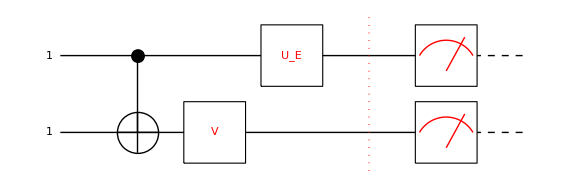

```mathematica
Let[Real,ϕ,a,b,c]
expr[1]=S[2,1]+I S[3,3];
qc=QuissoCircuit[
Ket[S[{1,2}]->1],
CNOT[S[1],S[2]],Red,
Rotation[S[2,3],ϕ,Label->"V"],
EulerRotation[S[1],{a,b,c}],
"Separator",
Measure[S[{1,2}]],
ImageSize->Large
]
```

```mathematica
expr[0]=QuissoExpression[qc]
vec[0]=Simplify@Matrix[qc];
vec[0]//MatrixForm
```

(Cos[b/2] 1_S_1 (Cos[(a+c)/2]+ⅈ Sin[(a+c)/2]) (Cos[ϕ/2]-ⅈ Sin[ϕ/2]))/(|Cos[b/2]|)

(-(Sin[b/2] (Cos[1/2 (a-c+ϕ)]-ⅈ Sin[1/2 (a-c+ϕ)]))/(|Sin[b/2]|)
0
0
0)

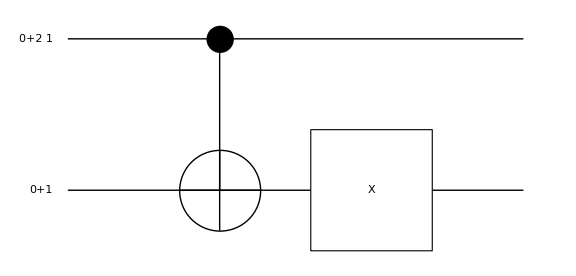

␣+2 1_S_1+2 1_S_11_S_2+1_S_2

(1
1
2
2)

```mathematica
qc=QuissoCircuit[
ProductState[S[1]->{1,2},S[2]->{1,1}],
CNOT[S[1],S[2]],
S[2,1],
ImageSize->Large
]
expr[0]=QuissoExpression[qc]
vec[0]=Matrix[qc];
vec[0]//MatrixForm
```

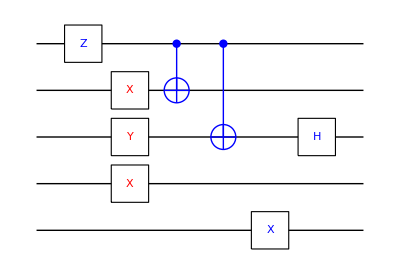

```mathematica
qc=QuissoCircuit[Blue,S[1,3],
{Red,S[2,1],S[3,2],S[4,1]},
{Blue, CNOT[S[1],S[2]] },
 CNOT[S[1],S[3]],
S[5,1],
S[3,6],
Opts->"A"
]
```

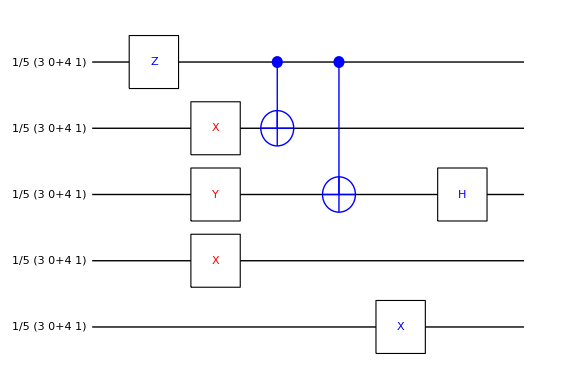

-Graphics-

{-(96 ⅈ √2)/3125,-(72 ⅈ √2)/3125,-(72 ⅈ √2)/3125,-(54 ⅈ √2)/3125,-(672 ⅈ √2)/3125,-(504 ⅈ √2)/3125,-(504 ⅈ √2)/3125,-(378 ⅈ √2)/3125,-(72 ⅈ √2)/3125,-(54 ⅈ √2)/3125,-(54 ⅈ √2)/3125,-(81 ⅈ)/(3125 √2),-(504 ⅈ √2)/3125,-(378 ⅈ √2)/3125,-(378 ⅈ √2)/3125,-(567 ⅈ)/(3125 √2),(96 ⅈ √2)/3125,(72 ⅈ √2)/3125,(72 ⅈ √2)/3125,(54 ⅈ √2)/3125,-(672 ⅈ √2)/3125,-(504 ⅈ √2)/3125,-(504 ⅈ √2)/3125,-(378 ⅈ √2)/3125,(128 ⅈ √2)/3125,(96 ⅈ √2)/3125,(96 ⅈ √2)/3125,(72 ⅈ √2)/3125,-(896 ⅈ √2)/3125,-(672 ⅈ √2)/3125,-(672 ⅈ √2)/3125,-(504 ⅈ √2)/3125}

```mathematica
qc=QuissoCircuit[
ProductState[S[{1,2,3,4,5}]->{3,4}/5],
Blue,S[1,3],
{Red,S[2,1],S[3,2],S[4,1]},
{Blue, CNOT[S[1],S[2]] },
 CNOT[S[1],S[3]],
S[5,1],
S[3,6],
Black
]
expr[0]=QuissoExpression[qc]
vec[0]=Simplify@Matrix[qc];
vec[0]//Normal
```

## Example with GraphStates

Let us consider the graph states.

```mathematica
Let[Qubit,S]
```

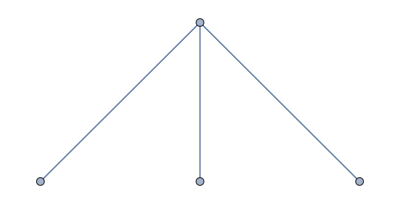

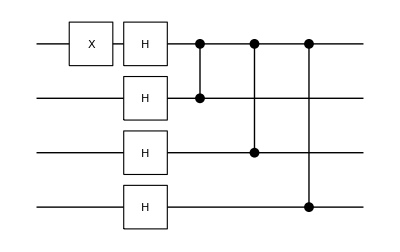

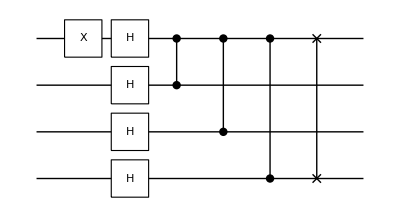

-Graphics-

```mathematica
g=Graph[{S[1]<->S[2],S[1]<->S[3],S[1]<->S[4]}]
qc=QuissoCircuit[S[1,1],g]
qc=QuissoCircuit[qc,SWAP[S[1],S[4]]]
QuissoExpand@QuissoExpression[qc]//Simplify
```

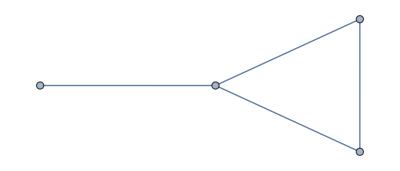

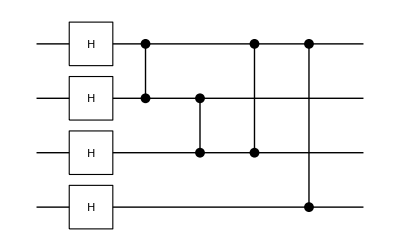

```mathematica
g=Graph[{S[1]<->S[2],S[2]<->S[3],S[1]<->S[3],S[1]<->S[4]}]
QuissoCircuit[g]
```

0_S_10_S_20_S_30_S_4

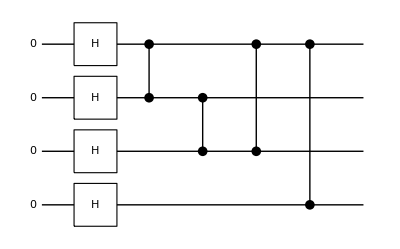

␣/4-1/4 1_S_11_S_2-1/4 1_S_11_S_21_S_3+(1_S_1)/4+1/4 1_S_11_S_21_S_31_S_4+1/4 1_S_11_S_21_S_4-1/4 1_S_11_S_3+1/4 1_S_11_S_31_S_4-1/4 1_S_11_S_4-1/4 1_S_21_S_3-1/4 1_S_21_S_31_S_4+(1_S_2)/4+1/4 1_S_21_S_4+(1_S_3)/4+1/4 1_S_31_S_4+(1_S_4)/4

{1/4,1/4,1/4,1/4,1/4,1/4,-1/4,-1/4,1/4,-1/4,-1/4,1/4,-1/4,1/4,-1/4,1/4}

1/4 (␣+1_S_1-1_S_11_S_2-1_S_11_S_21_S_3+1_S_11_S_21_S_31_S_4+1_S_11_S_21_S_4-1_S_11_S_3+1_S_11_S_31_S_4-1_S_11_S_4+1_S_2-1_S_21_S_3-1_S_21_S_31_S_4+1_S_21_S_4+1_S_3+1_S_31_S_4+1_S_4)

0

```mathematica
in=LogicalForm[Ket[],S[{1,2,3,4}]]
qc=QuissoCircuit[in,g]
v[1]=QuissoExpression[qc]
v[2]=Matrix[qc];
v[2]//Normal
v[3]=GraphState[g]
v[1]-v[3]//Simplify//Normal
```

## Examples with Measurements

Here are simple examples with measurements.

```mathematica
Let[Qubit,S]
```

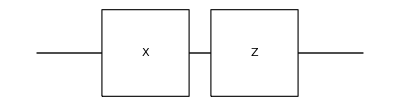

-1_S_1

```mathematica
qc=QuissoCircuit[Ket[],S[1,1],S[1,3]]
ex=QuissoExpression[qc]
```

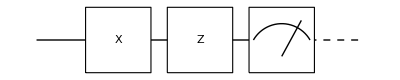

-1_S_1

```mathematica
qc=QuissoCircuit[Ket[],S[1,1],S[1,3],Measure[S[1]]]
ex=QuissoExpression[qc]
```

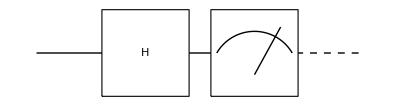

␣

```mathematica
qc=QuissoCircuit[Ket[],S[1,6],Measure[S[1]]]
ex=QuissoExpression[qc]
```

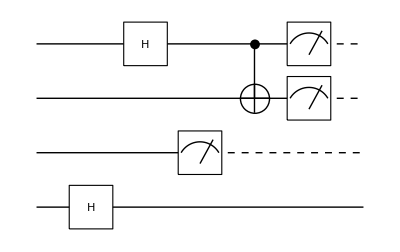

```mathematica
qc=QuissoCircuit[
Ket[],
S[4,6],S[1,6],
Measure[S[3]],
CNOT[S[1],S[2]],
{Measure[S[1]],Measure[S[2]]}
]
```

```mathematica
cc=(QuissoExpression@qc)//Simplify;
ccc=LogicalForm[cc,S[{1,2,3,4}]]
QuissoFactor[ccc,S[{1,2}]]
```

(0_S_10_S_20_S_30_S_4+0_S_10_S_20_S_31_S_4)/(√2)

0_S_10_S_2⊗((0_S_30_S_4+0_S_31_S_4)/(√2))

Take another example

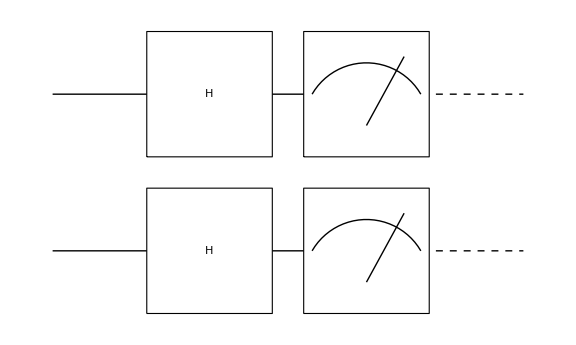

```mathematica
qc=QuissoCircuit[Ket[],{S[1,6],S[2,6]},{Measure[S[{1,2}]],Label->"M"},
ImageSize->Large]
```

```mathematica
data=Table[(result=QuissoExpression[qc];Readout[S[{1,2}],result]),{1000}];
Histogram3D[data,AxesLabel->{S[1,],S[2,],"Counts"}]
```

-Graphics3D-

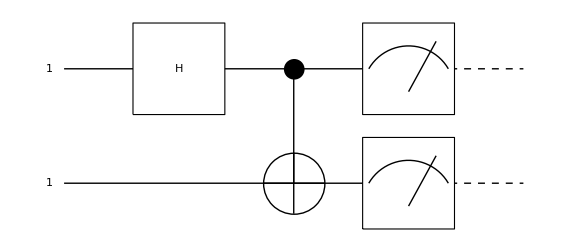

```mathematica
qc=QuissoCircuit[
Ket[S[{1,2}]->1],
S[1,6],CNOT[S[1],S[2]],
{Measure[S[1]],Measure[S[2]]},
ImageSize->Large
]
```

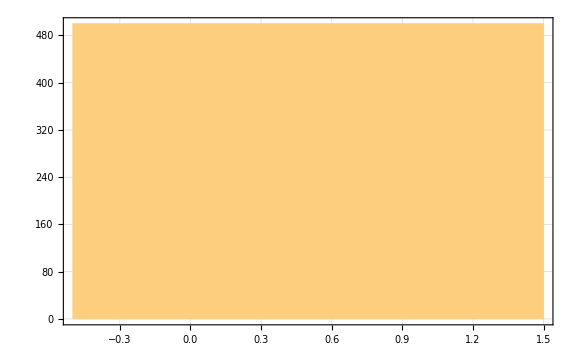

```mathematica
data=Table[(result=QuissoExpression[qc];Readout[S[1],result]),{1000}];
Histogram[data,Axes->False,Frame->True,FrameStyle->Large]
```

(0_S_11_S_2-1_S_10_S_2)/(√2)

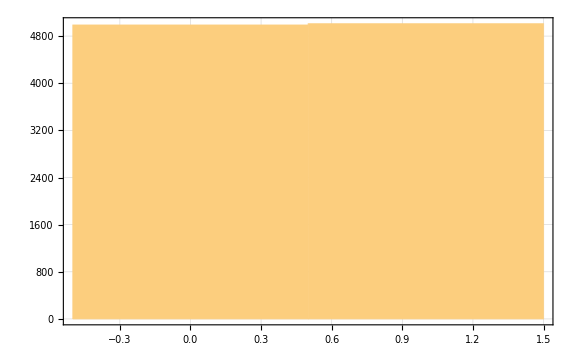

```mathematica
v=QuissoCNOT[S[1],S[2]]**S[1,6]**Ket[S[{1,2}]->1]//Simplify;
v//LogicalForm
data=Table[
u=Measure[S[1]][Measure[S[2]][v]];
Readout[S[1],u],
{j,10000}
];
Histogram[data]
```

## Examples with Controlled Gates

Here are simple examples involving controlled gates.

```mathematica
Let[Qubit,S]
```

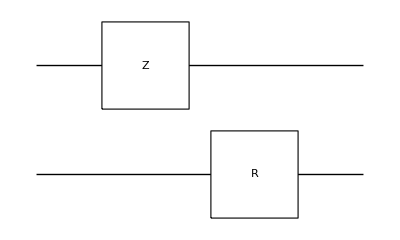

```mathematica
QuissoCircuit[
S[1,3],
Rotation[S[2,1],Pi/3,Label->"R"]]
```

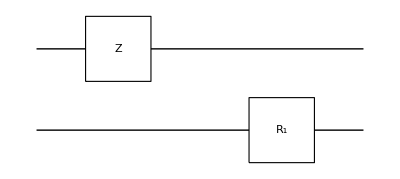

```mathematica
qc=QuissoCircuit[
S[1,3],Pi,
Rotation[S[2,1],Pi/3,Label->"R_1"]]
```

```mathematica
qc//QuissoExpression
```

-1/2 ⅈ π S_1^z S_2^x+1/2 √3 π S_1^z

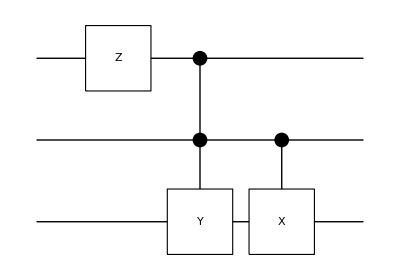

```mathematica
QuissoCircuit[
S[1,3],
Controlled[S[{1,2}],S[3,2]],
Controlled[S[2],S[3,1]]
]
```

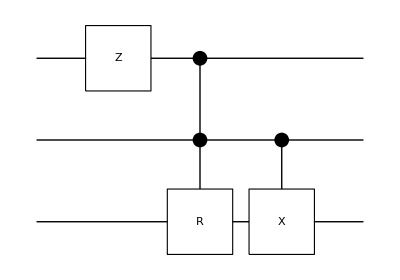

```mathematica
QuissoCircuit[
S[1,3],
Controlled[S[{1,2}],Rotation[S[3,2],Pi/3],Label->"R"],
Controlled[S[2],S[3,1]]
]
```

## Examples with Arbitrary Controlled Gates

```mathematica
Let[Qubit,S]
```

S_3^x-ⅈ S_3^y+S_4^z/2

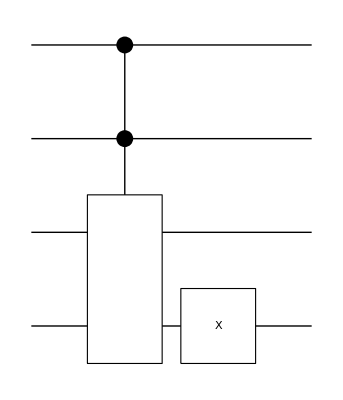

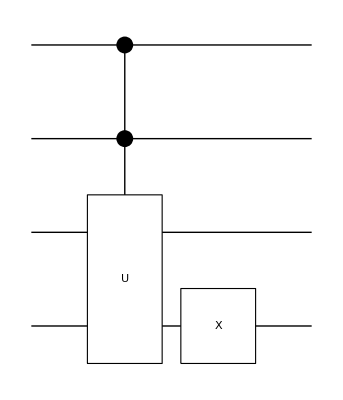

```mathematica
Clear[expr,qc];
expr=S[3,1]- I S[3,2] + S[4,3]/2
qc[1]=QuissoCircuit[Controlled[S[{1,2}],expr],S[4,1]]
qc[2]=QuissoCircuit[Controlled[S[{1,2}],expr,Label->"U"],S[4,1]]
```

```mathematica
ex[1]=QuissoExpression[qc[1]]//Simplify
ex[2]=QuissoExpression[qc[2]]//Simplify
ex[1]-ex[2]//Simplify
```

1/8 (2 S_1^z S_4^x+ⅈ (S_1^z S_4^y-2 ⅈ S_2^z S_4^x+S_2^z S_4^y-2 ⅈ S_3^x S_4^x-2 S_3^y S_4^x+2 ⅈ S_1^z S_2^z S_4^x-S_1^z S_2^z S_4^y+2 ⅈ S_1^z S_3^x S_4^x+2 S_1^z S_3^y S_4^x+2 ⅈ S_2^z S_3^x S_4^x+2 S_2^z S_3^y S_4^x-2 ⅈ S_1^z S_2^z S_3^x S_4^x-2 S_1^z S_2^z S_3^y S_4^x-6 ⅈ S_4^x-S_4^y))

1/8 (2 S_1^z S_4^x+ⅈ (S_1^z S_4^y-2 ⅈ S_2^z S_4^x+S_2^z S_4^y-2 ⅈ S_3^x S_4^x-2 S_3^y S_4^x+2 ⅈ S_1^z S_2^z S_4^x-S_1^z S_2^z S_4^y+2 ⅈ S_1^z S_3^x S_4^x+2 S_1^z S_3^y S_4^x+2 ⅈ S_2^z S_3^x S_4^x+2 S_2^z S_3^y S_4^x-2 ⅈ S_1^z S_2^z S_3^x S_4^x-2 S_1^z S_2^z S_3^y S_4^x-6 ⅈ S_4^x-S_4^y))

0

### Further Examples with Arbitrary Gates

The (multi-qubit) gate (operator) is expressed in a Quisso expression.

```mathematica
Let[Qubit,S]
```

S_3^0+ⅈ S_4^x

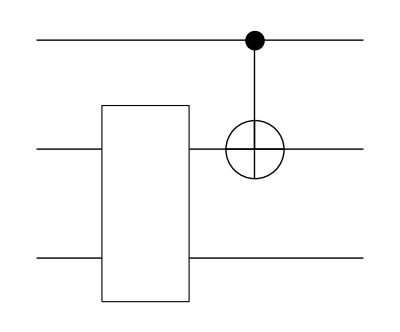

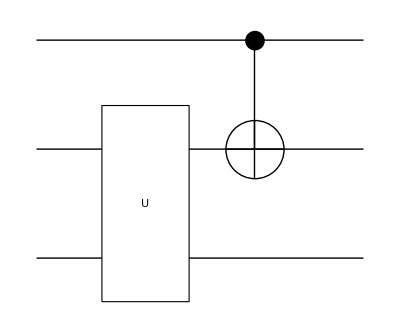

```mathematica
expr=S[3,0]+I S[4,1]
qc[1]=QuissoCircuit[ expr,CNOT[S[1],S[3]]]
qc[2]=QuissoCircuit[ {expr,Label->"U"},CNOT[S[1],S[3]]]
```

```mathematica
QuissoExpression[qc[1]]//QuissoExpand//Simplify
QuissoExpression[qc[2]]//QuissoExpand//Simplify
```

1/2 (1-S_1^z S_3^x+ⅈ S_1^z S_4^x+ⅈ S_3^x S_4^x-ⅈ S_1^z S_3^x S_4^x+S_1^z+S_3^x+ⅈ S_4^x)

1/2 (1-S_1^z S_3^x+ⅈ S_1^z S_4^x+ⅈ S_3^x S_4^x-ⅈ S_1^z S_3^x S_4^x+S_1^z+S_3^x+ⅈ S_4^x)

The gate is expressed in a matrix representation.

(ⅈ | 1
1 | -ⅈ)

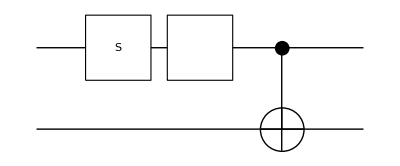

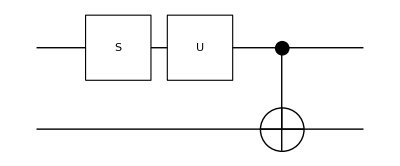

```mathematica
mat=ThePauli[1]+I ThePauli[3];mat//MatrixForm
op=QuissoExpression[mat,S[1]];
qc[1]=QuissoCircuit[S[1,7], op,CNOT[S[1],S[3]]]
qc[2]=QuissoCircuit[ S[1,7],{op,Label->"U"},CNOT[S[1],S[3]]]
```

```mathematica
ex[1]=qc[1]//QuissoExpression//QuissoExpand//Simplify
ex[2]=qc[2]//QuissoExpression//QuissoExpand//Simplify
ex[1]-ex[2]//Simplify
```

1/2 (ⅈ+S_1^x S_3^x-ⅈ S_1^y S_3^x-S_1^z S_3^x+ⅈ S_1^x-S_1^y+ⅈ S_1^z+S_3^x)

1/2 (ⅈ+S_1^x S_3^x-ⅈ S_1^y S_3^x-S_1^z S_3^x+ⅈ S_1^x-S_1^y+ⅈ S_1^z+S_3^x)

0

Multi-qubit gate is expressed in a matrix representation.

(0 | 0 | 0 | -ⅈ
0 | 0 | ⅈ | 0
0 | -ⅈ | 0 | 0
ⅈ | 0 | 0 | 0)

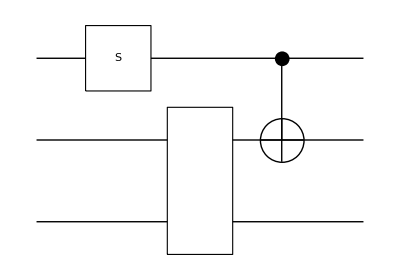

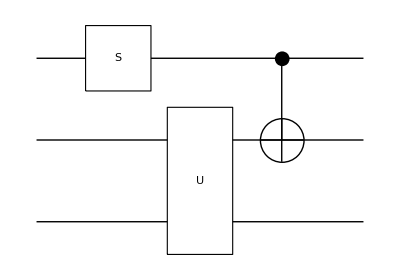

```mathematica
mat=ThePauli[1,2];mat//MatrixForm
qq=S[{3,4}];
op=QuissoExpression[mat,qq];
qc[1]=QuissoCircuit[S[1,7], op,CNOT[S[1],S[3]]]
qc[2]=QuissoCircuit[ S[1,7],{op,Label->"U"},CNOT[S[1],S[3]]]
```

```mathematica
QuissoExpression[qc[1]]//Simplify
QuissoExpression[qc[2]]//Simplify
```

1/2 (-ⅈ S_1^z S_4^y+S_3^x S_4^y+S_1^z S_3^x S_4^y+ⅈ S_4^y)

1/2 (-ⅈ S_1^z S_4^y+S_3^x S_4^y+S_1^z S_3^x S_4^y+ⅈ S_4^y)

## Quantum Fourier transform

The quantum Fourier transform algorithm is illustrated in a circuit.

```mathematica
Let[Qubit,S]
```

```mathematica
nn=Range[5];
qq=S[nn,]
```

{S_1,S_2,S_3,S_4,S_5}

```mathematica
CR[m_,n_,k_]:=Controlled[S[m],Phase[S[n],2Pi/2^k],Label->Subscript["R",m]]
```

```mathematica
Let[Integer,j]
Clear[v]
jj=j[nn];
jj=Ket/@jj;
v[1]=LogicalForm[Ket[],qq];
```

```mathematica
phase[k_]:=With[
{jj=j[nn]},
Row[{Ket[0],"+",Ket[1],Superscript["e",Row@Join[{"2π"," i ","0","."},Drop[jj,k-1]]]}]
]
ll=Array[phase,5]
v[2]=ProductState[S[nn]->{1,0}]
```

{0+1e^(2π i 0.j_1j_2j_3j_4j_5),0+1e^(2π i 0.j_2j_3j_4j_5),0+1e^(2π i 0.j_3j_4j_5),0+1e^(2π i 0.j_4j_5),0+1e^(2π i 0.j_5)}

(0)_S_1⊗(0)_S_2⊗(0)_S_3⊗(0)_S_4⊗(0)_S_5

Recall that unlike the seemingly general label, the example below is for a particular input.

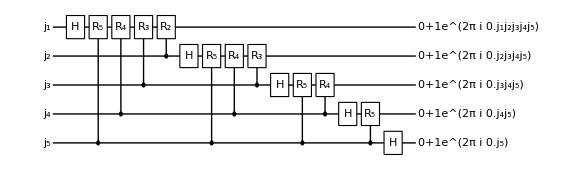

```mathematica
qc=QuissoCircuit[
{v[1],Label->jj},
S[1,6],CR[5,1,5],CR[4,1,4],CR[3,1,3],CR[2,1,2],
S[2,6],CR[5,2,4],CR[4,2,3],CR[3,2,2],
S[3,6],CR[5,3,3],CR[4,3,2],
S[4,6],CR[5,4,2],
S[5,6],
{v[2],Label->ll},
ImageSize->Large,
PlotRangePadding->{2,0}]
```

```mathematica
Timing[QuissoExpression[qc]//Simplify//LogicalForm[#,qq]&]
```

-Graphics-

## Matrix on QuissoCircuit

Depending on the ratio of the “size” (the number of qubits) and the “depth” (the number of operations), Matrix is more efficient than the QuissoExpression.

```mathematica
Let[Qubit,S]
```

```mathematica
$N=5;
ss=S[Range[$N],None]
```

{S_1,S_2,S_3,S_4,S_5}

```mathematica
CP[j_,j_]:=S[j,6]
CP[j_,k_]:=Controlled[S[j],
Phase[S[k],Pi Power[2,k-j],Label->Subscript["S",j-k]]
]/;j>k
CP[j_,k_]:=Controlled[S[j],
Phase[S[k],Pi Power[2,j-k],Label->Subscript["S",k-j]]
]/;j<k
SW[j_]:=SWAP[S[j],S[$N-j+1]]
```

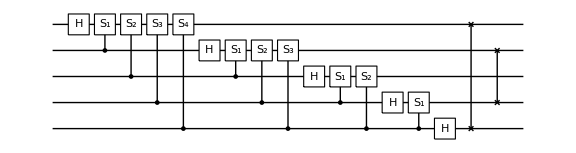

```mathematica
swaps=Table[SW[j],{j,1,$N/2}];
gates4a=Catenate@Table[CP[j,k],{k,1,$N},{j,k,$N}];
qft4a=Join[gates4a,swaps];
qc4a=QuissoCircuit[Sequence@@qft4a,ImageSize->Large]
```

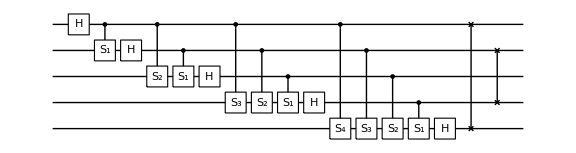

```mathematica
swaps=Table[SW[j],{j,1,$N/2}];
gates4b=Catenate@Table[CP[j,k],{k,1,$N},{j,1,k}];
qft4b=Join[gates4b,swaps];
qc4b=QuissoCircuit[Sequence@@qft4b,ImageSize->Large]
```

```mathematica
Timing[mat4a=Matrix[qc4a];]
Timing[mat4b=Matrix[qc4b];]
mat4a-mat4b//Simplify//Flatten//DeleteCases[#,0]&
Timing[mat4a=Matrix[qc4a];]
Timing[mat4b=Matrix[qc4b];]
mat4a-mat4b//Simplify//Normal//Flatten//DeleteCases[#,0]&
```

{0.687248,Null}

{0.655713,Null}

SparseArray[…]

{1.89704,Null}

{0.655789,Null}

{}

WARNING: The following takes quite long, sometime even fails, as the circuit is pretty deep compared with the size.

```mathematica
Timing[op4a=QuissoExpression[qc4a];]
```

{743.31,Null}

```mathematica
Timing[mat4c=Matrix[op4a];]
```

{0.371457,Null}

```mathematica
mat4a-mat4c//N//Chop//Normal
```

-Graphics-

## Matrix on QuissoCircuit: With Measure

Here we illustrate how Matrix works on a QuissoCircuitpaclet:Q3/ref/QuissoCircuit when it involves Measurepaclet:Q3/ref/Measure.

```mathematica
Let[Qubit,S]
```

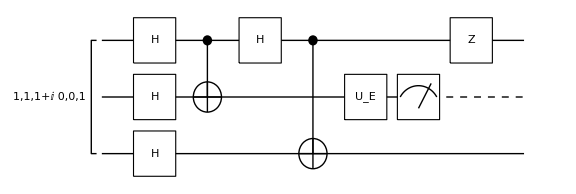

```mathematica
jj=Range[3];
ss=S[jj,];
gg={Ket[ss->1]+I Ket[S[3]->1],
S[jj,6],
CNOT[S[1],S[2]],S[1,6],
CNOT[S[1],S[3]],
EulerRotation[S[2],{Pi/3,Pi/2,Pi/3}],
Measure[S[2]],
S[1,3]};
qc=QuissoCircuit[Sequence@@gg,ImageSize->Large]
```

```mathematica
mat1=Matrix@qc//Simplify;
mat1//Normal
mat2=Matrix[QuissoExpression@qc,ss];
mat2//Normal
mat3=Matrix@qc//Simplify;
mat3//Normal
mat1-mat2//Simplify//Normal
mat2-mat3//Simplify//Normal
{Readout[S[2],QuissoExpression[mat1,ss]],
Readout[S[2],QuissoExpression[mat2,ss]]}
```

{((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),-((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),0,0,0,0,0,0}

{((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),-((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),0,0,0,0,0,0}

{((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),-((1/4-ⅈ/4) ((2+ⅈ)+√3))/(√(2+√3)),0,0,0,0,0,0}

{0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0}

{0,0}

Let us collect the measurement readouts to get the statistics.

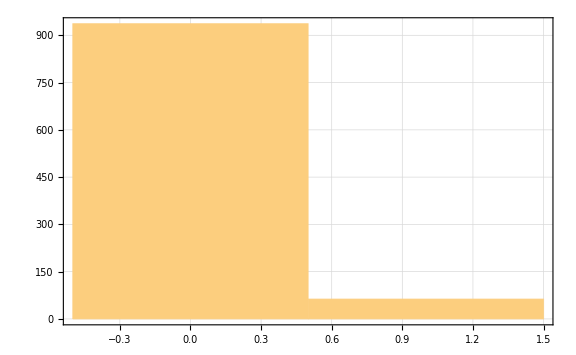

```mathematica
data1=Table[(
result=Matrix[qc];
Readout[S[2],QuissoExpression[result,ss]]
),1000];
Histogram[data1]
```

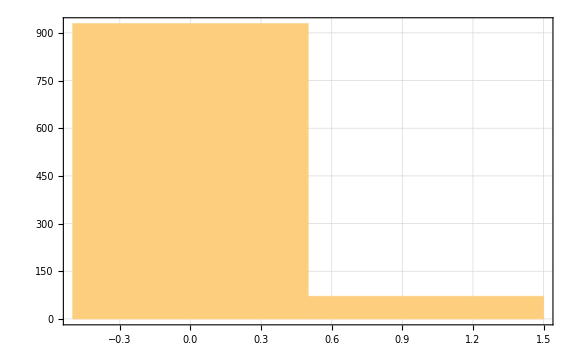

```mathematica
data2=Table[(result=QuissoExpression[qc];
Readout[S[2],result]),1000];
Histogram[data2]
```

Related Guides

Quissopaclet:Q3/guide/Quisso

Related Tutorials

Quissopaclet:Q3/tutorial/Quisso